# Fig. 4: Wigner Distributions

```mathematica
(*PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]*)
```

## 1. Packages and Fock-Space Cutoff

```mathematica
Needs[  "Wolfram`QuantumFramework`"];
```

```mathematica
Needs[  "Wolfram`QuantumFramework`SecondQuantization`"];
```

```mathematica
SetFockSpaceSize[ 80];
```

## 2. Photon-Added Cat State

```mathematica
a=AnnihilationOperator[];
```

```mathematica
psi[m_,r_,phi_,cphi_]:=psi[m,r,phi,cphi]=Nest[a["Dagger"],CatState[][<|α->N[r E^(I phi)],ϕ->N[cphi]|>],m]["Normalize"];
```

## 3. Displaced and Postselected States

```mathematica
displaced[m_,r_,phi_,cphi_,s_]:=displaced[m,r,phi,cphi,s]=DisplacementOperator[#][psi[m,r,phi,cphi]]["StateVector"]&/@{N[s]/2,-N[s]/2};
```

```mathematica
Phi[m_,r_,phi_,cphi_,s_,d1_,d2_]:=QuantumState[Normalize[{1+#,1-#}.displaced[m,r,phi,cphi,s]]&[E^(I N[d1]) Tan[N[d2]/2]],80];
```

## 4. Fixed Parameters

```mathematica
{r,phi,cphi,d1,d2}={1,Pi/2,Pi/2,Pi/2,8 Pi/9};
```

## 5. Wigner Distributions

### s = 0

```mathematica
W0=Table[WignerRepresentation[Phi[m,r,phi,cphi,0,d1,d2],{-5.,5.},{-5.,5.}],{m,0,2}];
```

### s = 1

```mathematica
W1=Table[WignerRepresentation[Phi[m,r,phi,cphi,1,d1,d2],{-5.,5.},{-5.,5.}],{m,0,2}];
```

### s = 2

```mathematica
W2=Table[WignerRepresentation[Phi[m,r,phi,cphi,2,d1,d2],{-5.,5.},{-5.,5.}],{m,0,2}];
```

## 6. Color Scale

```mathematica
wrange={-0.3,0.3};
```

```mathematica
seismicCF=Blend[{RGBColor[0,0,0.3],RGBColor[0,0,1],White,RGBColor[1,0,0],RGBColor[0.5,0,0]},Clip[Rescale[#,wrange],{0,1}]]&;
```

## 7. Panel Labels and Axis Ticks

```mathematica
labels = "("<>#<>")"&/@Alphabet[][[;;9]];
```

```mathematica
sVals = Quotient[Range[0,8],3];
```

```mathematica
axisSpec = Table[ {i > 6, Mod[ i, 3] == 1}, {i, 9}];
```

```mathematica
blankTicks=Join[{#,"",{0.023,0}}&/@Range[-4,4,2],{#,"",{0.01,0}}&/@Range[-5,5,0.5]];
```

## 8. Density-Plot Format

```mathematica
tnr=Style[#,#2,Bold,Black,FontFamily->"Times New Roman"]&;
makePlot[fun_,lab_,s_,{showX_,showY_}]:=With[{padL=If[showY,100,5],padB=If[showX,95,5]},DensityPlot[fun[x,p],{x,-5,5},{p,-5,5},PlotPoints->120,ColorFunction->seismicCF,ColorFunctionScaling->False,PlotRange->All,PlotRangePadding->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.2]],FrameTicks->{{If[showY,Automatic,blankTicks],blankTicks},{If[showX,Automatic,blankTicks],blankTicks}},FrameLabel->{{If[showY,Style["p",35,Bold,Black],None],None},{If[showX,Style["x",35,Bold,Black],None],None}},FrameTicksStyle->Directive[Black,Bold,30],LabelStyle->Directive[Black,Bold,1],Epilog->{Text[tnr[lab,40],Scaled[{0.13,0.88}]],Text[tnr[Row[{Style["s",Italic]," = ",s}],40],Scaled[{0.5,0.88}]]},AspectRatio->1,ImagePadding->{{padL,5},{padB,5}},ImageSize->{305+padL,305+padB}]];
```

## 9. Generate the Nine Panels

```mathematica
plots=MapThread[makePlot,{Join[W0,W1,W2],labels,sVals,axisSpec}];
```

## 10. Color Legend and Column Headers

```mathematica
legend=BarLegend[{seismicCF,wrange},LabelStyle->Directive[Black,Bold,25],LegendMarkerSize->{30,900},TicksStyle->Directive[Black,Bold,30]];
mHeaders=MapAt[Row[{Spacer[53],#}]&,tnr[Row[{Style["m",Italic]," = "<>ToString[#]}],32]&/@Range[0,2],1];
```

## 11. Assemble and Display Fig. 4

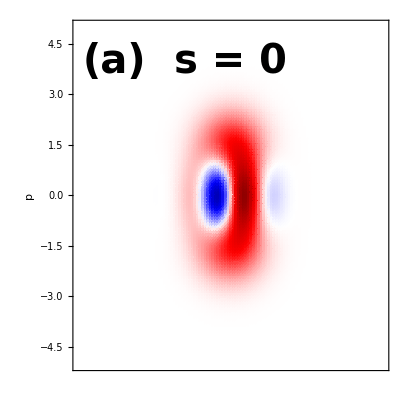
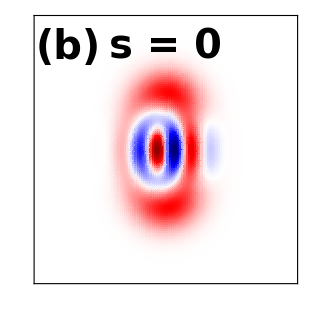
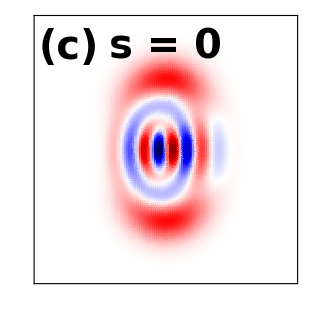
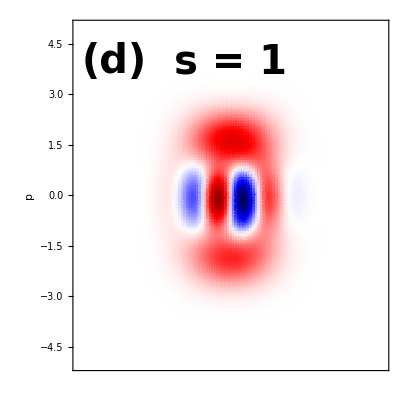
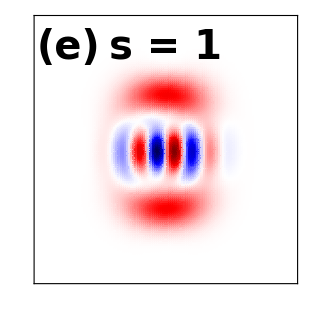
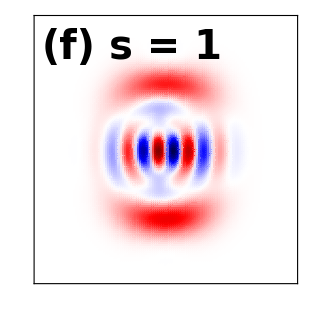
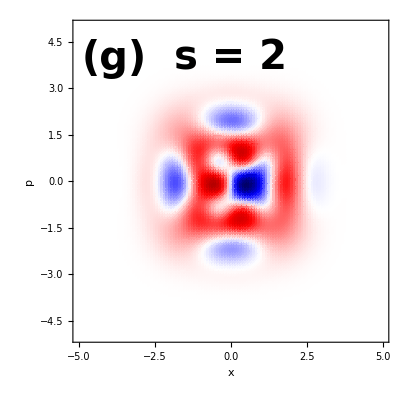
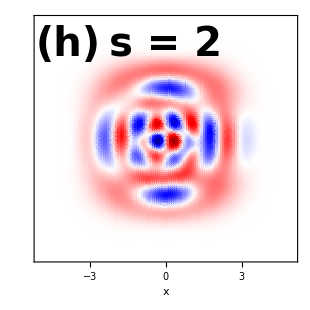
m = 0 | m = 1 | m = 2
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
b=Grid[{{Grid[Prepend[Partition[plots,3],mHeaders],Spacings->{0.,0.},Alignment->{Center,Center}],legend}},Spacings->{0.05,0},Alignment->{Center,Center}]
```

## 12. Export PNG (Optional)

```mathematica
(*Export[ FileNameJoin[ {NotebookDirectory[ ], "Fig.4_Concise.png"}], ImageCrop[ Rasterize[ b, "Image", RasterSize -> 4200, Background -> White]], "PNG"];*)
```